In this notebook, we calculate the local selection gradient for our model with assortative interactions studied in Section B.3 in the appendix. These calculations are used to produce Equation (B.14), which, in turn, is used to calculate the evolutionarily stable sociality strategy for a given assortment probability ρ.

First, we introduce the equilibrium level of contagion I_M for the rare mutant population with sociality strategy corresponding to reproduction number M for the good contagion, given the resident level of sociality strategy with reproduction number R for the good contagion. This expression was calculated in the adaptive dynamics limit for the good contagion in Equation (B.12) and for the bad contagion in Equation (B.13).

```mathematica
ImMinus[M_,R_,ρ_] := 1/(2 M ρ)(-1+M-2 M ρ-√((-1-M+2 M ρ+M/R-(M ρ)/R)^2+4 M ρ (M-M ρ-M/R+(M ρ)/R))-M/R+(M ρ)/R)
```

Next, we compute the Cobb-Douglas utility for the mutant population given the equilibrium levels of the good and bad contagion.

```mathematica
Utility[M_,R_,ρ_,α_,c_]:= α Log[ImMinus[M,R,ρ]] + (1 - α) Log[1 - ImMinus[c M,c R,ρ]]
```

To calculate the local selection gradient, we first differentiate the utility for mutant individuals with respect to the mutant reproduction number M, given a fixed resident reproduction number R.

```mathematica
D[Utility[M,R,ρ,α,c],M]
```

(2 M α ρ (1/(2 M ρ)(1-1/R-2 ρ+ρ/R-(4 M ρ (1-1/R-ρ+ρ/R)+2 (-1+1/R+2 ρ-ρ/R) (-1-M+M/R+2 M ρ-(M ρ)/R)+4 ρ (M-M/R-M ρ+(M ρ)/R))/(2 √((-1-M+M/R+2 M ρ-(M ρ)/R)^2+4 M ρ (M-M/R-M ρ+(M ρ)/R))))-1/(2 M^2 ρ)(-1+M-M/R-2 M ρ+(M ρ)/R-√((-1-M+M/R+2 M ρ-(M ρ)/R)^2+4 M ρ (M-M/R-M ρ+(M ρ)/R)))))/(-1+M-M/R-2 M ρ+(M ρ)/R-√((-1-M+M/R+2 M ρ-(M ρ)/R)^2+4 M ρ (M-M/R-M ρ+(M ρ)/R)))+((1-α) (-1/(2 c M ρ)(c-1/R-2 c ρ+ρ/R-(4 c M ρ (c-1/R-c ρ+ρ/R)+2 (-c+1/R+2 c ρ-ρ/R) (-1-c M+M/R+2 c M ρ-(M ρ)/R)+4 c ρ (c M-M/R-c M ρ+(M ρ)/R))/(2 √((-1-c M+M/R+2 c M ρ-(M ρ)/R)^2+4 c M ρ (c M-M/R-c M ρ+(M ρ)/R))))+1/(2 c M^2 ρ)(-1+c M-M/R-2 c M ρ+(M ρ)/R-√((-1-c M+M/R+2 c M ρ-(M ρ)/R)^2+4 c M ρ (c M-M/R-c M ρ+(M ρ)/R)))))/(1-1/(2 c M ρ)(-1+c M-M/R-2 c M ρ+(M ρ)/R-√((-1-c M+M/R+2 c M ρ-(M ρ)/R)^2+4 c M ρ (c M-M/R-c M ρ+(M ρ)/R))))

To further calculate the local selection gradient, we evaluate the derivative of the mutant utility with respect to mutant reproduction number M for the case in which the mutant and resident reproduction numbers coincide (M = R). This allows us to see whether utility will increase or decrease for a mutant with sociality strategy near the resident sociality strategy.

```mathematica
D[Utility[M,R,ρ,α,c],M] /.{M->R} //FullSimplify
```

1/R(-(α (R+√((R-ρ)^2)+ρ-2 R ρ))/(√((R-ρ)^2) (2+√((R-ρ)^2)-ρ+R (-1+2 ρ)))+((-1+α) (ρ+√((-c R+ρ)^2)+c (R-2 R ρ)))/(√((-c R+ρ)^2) (2-ρ+√((-c R+ρ)^2)+c R (-1+4 ρ))))

We can simplify the expression for the local selection gradient using the fact that reproduction numbers for the good contagion always satisfy R >= 1. In addition, we will assume that cR > ρ, which simplifies our expression. This second assumption is justified if we restrict attention to cases in which the socially optimal sociality strategy is achieved at a critical point of the monomorphic utility function (i.e. R_{opt} > 1 / c, which occurs when c > 1 - α).

```mathematica
FullSimplify[-1/(2 R)((-2+c R+ρ+√((-c R+ρ)^2))/(√((-c R+ρ)^2))+α (-1-2/(√((R-ρ)^2))+2/(√((-c R+ρ)^2))-(c R+ρ)/(√((-c R+ρ)^2)))),{R-ρ > 0, c R - ρ > 0}]
```

```mathematica
(α/(R-ρ)+((-1+c R) (-1+α))/(c R-ρ))/R
```

(α/(R-ρ)+((-1+c R) (-1+α))/(c R-ρ))/R

In the next two steps, we simplify the expression for the local selection gradient to obtain the formula presented in Equation (B.14) in the appendix.

```mathematica
Together[(α/(R-ρ)+((-1+c R) (-1+α))/(c R-ρ))/R]
```

(R-c R^2-R α+c R α+c R^2 α-ρ+c R ρ-c R α ρ)/(R (R-ρ) (c R-ρ))

```mathematica
Collect[R-c R^2-R α+c R α+c R^2 α-ρ+c R ρ-c R α ρ,R] /(R (R-ρ) (c R-ρ))
```

(R^2 (-c+c α)-ρ+R (1-α+c α+c ρ-c α ρ))/(R (R-ρ) (c R-ρ))

Next, we set the selection gradient equal to zero to calculate the evolutionarily stable sociality strategy for a given assortment probability ρ. We can use the fact that the numerator of the selection gradient is a decreasing function of R to see that the positive root (listed second) is the unique ESS.

```mathematica
Solve[(α/(R-ρ)+((-1+c R) (-1+α))/(c R-ρ))/R==0,R]
```

{{R→1/(2 (-c+c α))(-1+α-c α-c ρ+c α ρ-√(4 (-c+c α) ρ+(1-α+c α+c ρ-c α ρ)^2))},{R→1/(2 (-c+c α))(-1+α-c α-c ρ+c α ρ+√(4 (-c+c α) ρ+(1-α+c α+c ρ-c α ρ)^2))}}

Introducing shorthand to calculate the regions in which the local selection gradient is positive or negative (given assortment probability ρ).

```mathematica
G[R_,p_,c_,α_]:=-1/(2 R)((-2+c R+ρ+√((-c R+ρ)^2))/(√((-c R+ρ)^2))+α (-1-2/(√((R-ρ)^2))+2/(√((-c R+ρ)^2))-(c R+ρ)/(√((-c R+ρ)^2))))
```

Plot of regions in which local selection gradient is increasing (filled in blue) and decreasing (filled in orange) depending on the resident sociality reproduction number R and the assortment probability ρ. The boundary between the regions corresponds to the ESS sociality strategy. In first plot, we consider case in which c = 1/2, so the ESS with no assortative interactions (ρ = 0) features more interactions than experienced by the socially optimal sociality strategy.

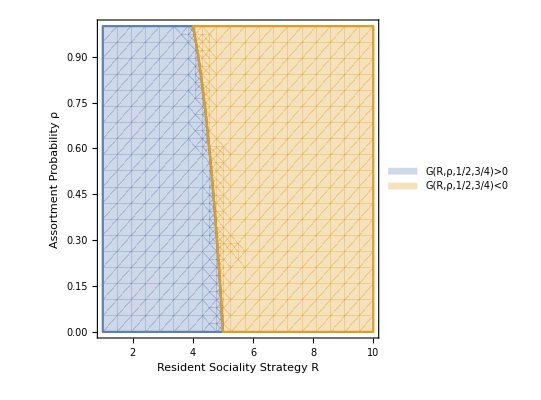

```mathematica
RegionPlot[{G[R,ρ,1/2,3/4]> 0 , G[R,ρ,1/2,3/4]< 0},{R,1,10},{ρ,0,1},PlotLegends->"Expressions", FrameLabel->{ Style["Resident Sociality Strategy R",16],Style["Assortment Probability ρ" , 16]}]
```

In second plot, we consider case in which c = 2, so the ESS with no assortative interactions (ρ = 0) features fewer interactions than experienced by the socially optimal sociality strategy.

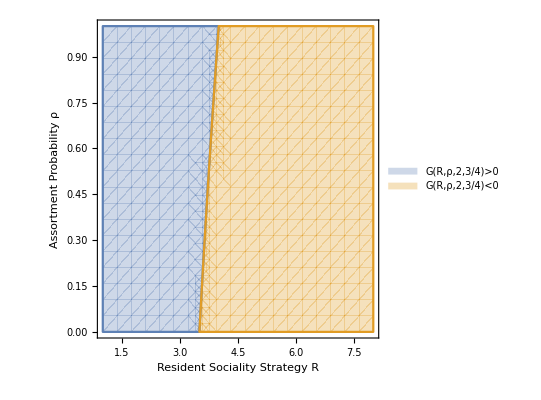

```mathematica
RegionPlot[{G[R,ρ,2,3/4]> 0 , G[R,ρ,2,3/4]< 0},{R,1,8},{ρ,0,1},PlotLegends->"Expressions", FrameLabel->{ Style["Resident Sociality Strategy R",16],Style["Assortment Probability ρ" , 16]}]
```